```mathematica
(* This module creates a K-M curve using the given filename *)
dir=NotebookDirectory[]<>"runData/";
makeSurvivalCurve[filename_]:=Module[
{data,patients,time,ci,S},
data=Import[dir<>filename,"Data"];
patients = data[[4;;]]; (* The first 3 lines contain parameter info *)
time={};
(* We now loop over all patients and look to see when progression occurs (we add large number to cure so it will never show progression in the K-M curve). *)
For[n=1,n≤ Length[patients],n++,
If[patients[[n,2]]=="cure",AppendTo[time,patients[[n,1]]+10000],AppendTo[time,patients[[n,1]]]]];
ci=0&/@Range[Length[time]];
S=SurvivalModelFit[EventData[time,ci]];
{time,ci,patients,S}
]
```

```mathematica
nStart=1;
nEnd=40;
nFiles = nEnd-nStart+1;
date="2019-12-23";
tumorBurdenSurvivalCurves=makeSurvivalCurve["outputData_"<>ToString[#]<>"_"<>date<>".txt"]⟦4⟧&/@Range[nStart,nEnd];
```

```mathematica
days={"100 days","200 days","400 days","800 days"};
```

```mathematica
tumorBurdenPFSday[day_]:={# 0.5,(tumorBurdenSurvivalCurves[[#]][day])}&/@Range[1,nFiles];
```

```mathematica
(* This function makes a survival curve as a function of the initial tumor burden *)
L1[SurvivalCurve_,c_,i_]:=ListPlot[SurvivalCurve,
PlotRange->{{0,20.5},{0,1.05}},
(*GridLines->{{},{1.0}},*)
PlotStyle->Directive[c,PointSize->0.025],
LabelStyle->{Black,FontSize->18,FontFamily->"Arial"}
,Frame->{{True,False},{True,False}}
,AspectRatio->0.375
,ImageSize->500
,FrameStyle->Directive[Thickness[0.0035],Black]
,LabelStyle->{FontSize->18,Black,FontFamily->"Arial"}
, FrameLabel->{"Initial Tumor Burden","Probability of CR"},
PlotLegends->Placed[SwatchLegend[{days[[i]]},LegendMarkerSize->10,LegendMarkers->"Bubble",LegendLayout->{"Row",1}],Above]
];
```

```mathematica
tumorBurdenPFS ={ L1[tumorBurdenPFSday[100],ColorData["Rainbow"][0.1],1],L1[tumorBurdenPFSday[200],ColorData["Rainbow"][0.35],2],L1[tumorBurdenPFSday[400],ColorData["Rainbow"][0.6],3],L1[tumorBurdenPFSday[800],ColorData["Rainbow"][0.85],4]};
```

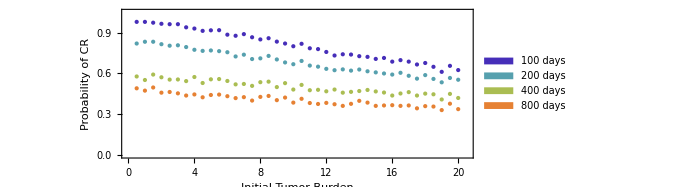

```mathematica
figTumorBurden=Show[tumorBurdenPFS]
```

```mathematica
Export[NotebookDirectory[]<>"TumorBurdenPFS.pdf",figTumorBurden,"PDF"]
```

/Users/gregorykimmel/Dropbox/_Projects/01_CART/code/hybridModelRuns/TumorBurdenPFS.pdf

```mathematica
(* Errorbars?? *)
```

```mathematica
stdDeviation[initBurden_]:=√(1/1000 tumorBurdenSurvivalCurves[[initBurden]][100](1-tumorBurdenSurvivalCurves[[initBurden]][100]))
```

```mathematica
Needs["ErrorBarPlots`"];
```

```mathematica
blah=tumorBurdenPFSday[100];
```

```mathematica
blah2={blah[[#]],ErrorBar[3*stdDeviation[#]]}&/@Range[1,Length[blah]];
```

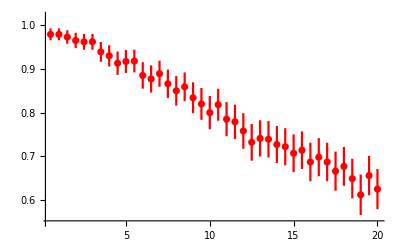

```mathematica
ErrorListPlot[blah2,PlotStyle->Red,PlotRange->{Full,{0.55,1.02}}]
```